#### EoS check

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\PythonTemp\NSPBGW\code00

```mathematica
Msun=1.98847*10^30;                      (* Mass of the sun*)
Mpc=3.085677581*10^22;               (* million par second *)
pc=3.085677581*10^16;                  (* parsecond *)
ly=365*3600*24*c;                          (* light year *)
Mly=10^6*365*24*3600*c;          (* million light year *)
H0=67.9*10^3/Mpc;                    (* Hubble constant *)
c=299792458;                                 (* Speed of light *)
Gn=6.67408*10^-11;(* Gravitational constant *)    
ρs=7.86*10^3;(*ρFe=7.86*10^3 kg/m^3*)
mn=1.4Msun; 
yt=365*3600*24;(* the NS parameters*)
```

### 1 states of NS

```mathematica
a1=3.916;        b1=4.078;             c1= 4.857;
a2=7.701;        b2= 7.587;            c2= 6.981;
a3=0.00858;   b3= 0.00839;        c3= 0.00706;
a4=0.22114;   b4= 0.21695;        c4= 0.19351;
a5=3.269;        b5= 3.614;            c5= 4.085;
a6=11.964;      b6= 11.942;         c6= 12.065;
a7=13.349;      b7= 13.751;         c7= 10.521;
a8=1.3683;      b8= 1.3373;         c8= 1.5905;
a9=3.254;        b9= 3.606;            c9= 4.104;
a10=−12.953; b10=−22.996;     c10=−28.726;
a11=0.9237;    b11= 1.6229;       c11= 2.0845;
a12=6.20;         b12= 4.88;           c12= 4.89;
a13=14.383;    b13= 14.274;       c13= 14.302;
a14=16.693;    b14= 23.560;       c14= 22.881;
a15=−1.0514; b15=−1.5564;     c15=−1.7690;
a16=2.486 ;     b16=2.095;          c16= 0.989;
a17=15.362 ;   b17=15.294;       c17= 15.313;
a18=0.085;      b18= 0.084;        c18= 0.091;
a19=6.23;        b19= 6.36;           c19= 4.68;
a20=11.68;      b20= 11.67;        c20= 11.65;
a21=−0.029;   b21=−0.042;      c21=−0.086;
a22=20.1;        b22= 14.8;           c22= 10.0;
a23=14.19;      b23= 14.18;        c23= 14.15;
```

#### BSK19

```mathematica
ra=10.74*10^3;
(*rb=11.74*10^3;
rc=12.57*10^3;*)
ξa=Log10[ρa1];
ks=(a1+a2 ξa+a3 ξa^3)/(1+a4 ξa)(Exp[a5(ξa-a6)]+1)^-1+(a7+a8 ξa)(Exp[a9(a6-ξa)]+1)^-1+(a10+a11 ξa)(Exp[a12(a13-ξa)]+1)^-1+(a14+a15 ξa)(Exp[a16(a17-ξa)]+1)^-1+a18(1+(a19(ξa-a20))^2)^-1+a21(1+(a22(ξa-a23))^2)^-1/.ρa1->10^-3 ρs;
ps=0.1*10^ks;
ζ[ρ_]:=(a1+a2 ξ[ρ]+a3 ξ[ρ]^3)/(1+a4 ξ[ρ])(Exp[a5(ξ[ρ]-a6)]+1)^-1+(a7+a8 ξ[ρ])(Exp[a9(a6-ξ[ρ])]+1)^-1+(a10+a11 ξ[ρ])(Exp[a12(a13-ξ[ρ])]+1)^-1+(a14+a15 ξ[ρ])(Exp[a16(a17-ξ[ρ])]+1)^-1+a18(1+(a19(ξ[ρ]-a20))^2)^-1+a21(1+(a22(ξ[ρ]-a23))^2)^-1
ξ[ρ_]:=Log10[10^-3 ρ];
pa[ρ_]:=10^ ζ[ρ]/10;
```

```mathematica
(* equation for the p,ρ,m*)
dpadρ[ρ_]:=Evaluate[D[pa[ρ],ρ]];
(*dpadr[r_]:=-(ρ[r]+pa[ρ[r]]/c^2)(Gn( m[r]+4π r^3 pa[ρ[r]]/c^2))/(r(r-2 Gn m[r]/c^2));*)
dpadr[r_]:=-(Gn m[r]ρ[r])/r^2;
dρdr[r_]:=dpadr[r] dpadρ[ρ[r]]^-1;
dmr[r_]:=4π r^2 ρ[r];
```

```mathematica
Res=Flatten[NDSolve[{m'[r]==dmr[r],ρ'[r]==dρdr[r],
ρ[10^-15]==1.67846125*10^14 ρs,m[10^-15]==0},{m,ρ},
{r,10^-15,10740.000006875976},
MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12]]
```

{m→InterpolatingFunction[…],ρ→InterpolatingFunction[…]}

```mathematica
m1[r_]=m[r]/.Res;
ρ1[r_]=ρ[r]/.Res;
dm1dr[r_]:=4π r^2 ρ1[r];
dρ1dr[r_]:=dpadr[r] dpadρ[ρ[r]]^-1/.Res;
p1[r_]:=pa[ρ1[r]];
(* test*)
```

```mathematica
(*ra=r/.FindRoot[ρ1[r]==7860,{r,10740}]*)
ra = 10740.00000687934;
```

```mathematica
{m1[10740.000006862]/Msun,ρ1[ra],ρ1[10740.000006862]}
{m1[10740.000006875976]/Msun,ρ1[ra],ρ1[10740.000006875976],ρ1[10740.00000687934]}
```

{1.39814,73331.3,11166.8}

{1.39814,73331.3,8769.81,7860.17}

```mathematica
β1[r_]:=1/2 Log[(1-(2Gn m1[r])/(r c^2))^-1];
(*dα1dr[r_]:=(Gn (m1[r]+4π r^3 p1[r]/c^2))/(r^2 c^2(1-2Gn m1[r]/(r c^2)));*)
dα1dr[r_]:=(Gn m1[r])/(r^2 c^2);
(* the β1,B1 parameters can be directly calculate *)
B1[r_]:=(1-(2Gn m1[r])/(r c^2))^-1;
α1ra=1/2 Log[1-(2Gn m1[ra])/(ra c^2)]
NDSolve[{α'[r]==dα1dr[r],α[ra]==α1ra},{α},
{r,10^-10,ra},
MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12];
α1[r_]=α[r]/.%[[1,1]];
```

-0.526271

```mathematica
Export[ "Newtonmodel0alpha.txt", Table[N[{10^logr,α1[10^logr],dα1dr[10^logr]},16],{logr,-15,Log10[ra],20/10000}],"Table"]
Export[ "Newtonmodel0m.txt", Table[N[{10^logr,m1[10^logr],dm1dr[10^logr]},16],{logr,-15,Log10[ra],20/10000}],"Table"]
Export[ "Newtonmodel0rho.txt", Table[N[{10^logr,ρ1[10^logr],dρ1dr[10^logr]},16],{logr,-15,Log10[ra],20/10000}],"Table"]
```

Newtonmodel0alpha.txt

Newtonmodel0m.txt

Newtonmodel0rho.txt

```mathematica
rk=10739.9999
ρk=ρ1[rk]
mk=m1[rk]
```

10740.

243221.

2.78015×10^30

```mathematica
(*Clear[rk,ρk,mk]*)
```

```mathematica
NDSolve[{m'[r]==dmr[r],ρ'[r]==dρdr[r],
ρ[rk]==ρk,m[rk]==mk},{m,ρ},
{r,0.1,rk},
MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12]
```

{{m→InterpolatingFunction[…],ρ→InterpolatingFunction[…]}}

```mathematica
mk1[r_]=m[r]/.m->InterpolatingFunction[…];
ρk1[r_]=ρ[r]/.ρ->InterpolatingFunction[…];
pk1[r_]:=pa[ρk1[r]];
(* test*)
```

```mathematica
Plot[{m1[r]/Msun},{r,1,10000},PlotTheme->"Detailed"]
```

```mathematica
Plot[{m1[r]/Msun,mk1[r]/Msun},{r,1,10000},PlotTheme->"Detailed"]
```

```mathematica
Plot[{ρ1[r],ρk1[r]},{r,1,10000},PlotTheme->"Detailed"]
```

```mathematica
Plot[{p1[r],pk1[r]},{r,1,10000},PlotTheme->"Detailed"]
```

### 2 evolution equations

```mathematica
β1[r_]:=(1/2)Log[(1-(2Gn m1[r])/(r c^2))^-1];
dα1dr[r_]:=(Gn (m1[r]+4π r^3 p1[r]/c^2))/(r^2 c^2(1-2Gn m1[r]/(r c^2)));
(* the β1,B1 parameters can be directly calculate *)
B1[r_]:=(1-(2Gn m1[r])/(r c^2))^-1;
α1ra=(1/2)Log[1-(2Gn m1[ra])/(ra c^2)];
```

```mathematica
NDSolve[{α'[r]==dα1dr[r],α[ra]==α1ra},{α},
{r,10^-8,ra},
MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12]
```

{{α→InterpolatingFunction[…]}}

```mathematica
α1[r_]=α[r]/.α->InterpolatingFunction[…];
```

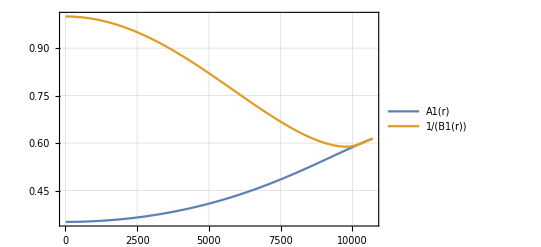

```mathematica
A1[r_]:=Exp[2α1[r]];
Plot[{A1[r],1/B1[r]},{r,10,10700},PlotRange->Full,PlotTheme->"Detailed"]
```

```mathematica
Plot[α1[r],{r,10,10700},PlotRange->Full,PlotTheme->"Detailed"]
Plot[dα1dr[r],{r,10,10700},PlotRange->Full,PlotTheme->"Detailed"]
```

```mathematica
ω1[r_]=c(dα1dr[r] A1[r]/r)^(1/2);
v1[r_]=ω1[r]r;
```

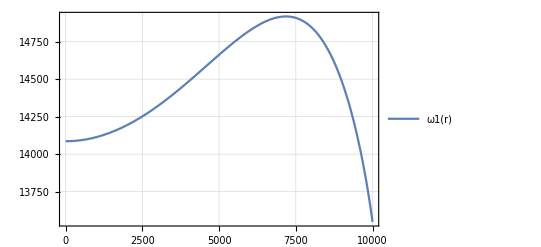

```mathematica
Plot[ω1[r],{r,1,10000},PlotTheme->"Detailed"]
```

```mathematica
ddα1ddr[r_]:=Evaluate[D[dα1dr[r],r]];
dB1dr[r_]:=Evaluate[D[B1[r],r]];
orbE[r_](*=ⅆt/ⅆτ A1[r]*)=√(A1[r]/(1-r dα1dr[r]))c^2;
doEdr[r_]=(3  dα1dr[r]-2 r  dα1dr[r]^2+r  ddα1ddr[r])/(2(1- r dα1dr[r]))√(A1[r]/(1-r dα1dr[r]));
orbE1[t_](*=ⅆt/ⅆτ A1[r]*)=√(A1[r[t]]/(1-r[t] dα1dr[r[t]]))c^2;
doEdt[t_]=doEdr[r[t]]r'[t] c^2;
```

```mathematica
cs1[r_]=(dpadρ[ρ1[r]])^(1/2);
calM[r_]=v1[r]/ cs1[r];
(*Iϕ1[r_]=Piecewise[{{0.7706Log[(1+calM[r])/(1.0004-0.9185calM[r])]-1.4703calM[r],calM[r]<1.0},{Log[3300(calM[r]-0.71)^5.72 calM[r]^-9.58],1.0<=calM[r]<4.4},{Log[10/(0.11calM[r]+1.65)],4.4<=calM[r]}}];*)
Iϕ1[r_]=Piecewise[{{calM[r]^3/3-0.80352calM[r]^4+7.68585calM[r]^5,calM[r]<0.08588},{0.7706Log[(1+calM[r])/(1.0004-0.9185calM[r])]-1.4703calM[r],0.08588<=calM[r]<1.0},{Log[3300(calM[r]-0.71)^5.72 calM[r]^-9.58],1.0<=calM[r]<4.4},{Log[10/(0.11calM[r]+1.65)],4.4<=calM[r]}}];

Ir1[r_]=Piecewise[{{calM[r]^2 10^(3.51calM[r]-4.22),calM[r]<1.1},{0.5Log[9.33 calM[r]^2(calM[r]^2-0.95)],1.1<=calM[r]<4.4},{0.3 calM[r]^2,4.4<=calM[r]}}];
```

```mathematica
fr1[t_]=(*-(M*m[r])/(Mcs*r^2)*)(-4π ρ1[r[t]] Gn^2 mp[t]^2/v1[r[t]]^2)Iϕ1[r[t]];
fr2[t_]=(*-(M*m[r])/(Mcs*r^2)*)(-4π ρ1[r[t]] Gn^2 1/v1[r[t]]^2)Ir1[r[t]]mp[t]/c^2;(*fr2/mp in geometirc *)
dfr2dr[t_]=Evaluate[D[(-4π ρ1[r[t]] Gn^2 1/v1[r[t]]^2)Ir1[r[t]],r[t]]]mp[t]/c^2+(-4π ρ1[r[t]] Gn^2 1/v1[r[t]]^2)Ir1[r[t]]mp'[t]/(c^2 r'[t]);
```

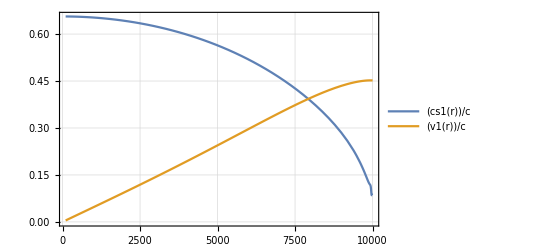

```mathematica
Plot[{cs1[r]/c,v1[r]/c},{r,100,10000},PlotTheme->"Detailed"]
```

```mathematica
{calM[100],calM[200],calM[500],calM[1000]}
{Ir1[100],Ir1[200],Ir1[500],Ir1[1000]}
{Iϕ1[100],Iϕ1[200],Iϕ1[500],Iϕ1[1000]}
```

{0.0071598,0.0143227,0.0358609,0.0721111}

{3.2729×10^-9,1.38779×10^-8,1.03542×10^-7,5.61196×10^-7}

{1.20377×10^-7,9.50204×10^-7,0.0000144994,0.000118252}

```mathematica
ut[t_]=√((2B1[r[t]]fr2[r[t]]-2/r[t])/(A1'[r[t]]-2A1[r[t]]/r[t]))c^2;
uϕ[t_]=√((A1[r[t]]ut[r[t]] ut[r[t]]-1)/r[t]^2);
ωt[t_]=uϕ[t]/ut[t];
```

```mathematica
orbE2[r_](*=ⅆt/ⅆτ A1[r]=A1[r] √((2B1[r]fr2[r]-2/r)/(A1'[r]-2A1[r]/r))*)=√((A1[r](B1[r]fr2[r]r-1))/(r dα1dr[r]-1))c^2;

orbEt2[t_](*=ⅆt/ⅆτ A1[r]=A1[r] √((2B1[r]fr2[r]-2/r)/(A1'[r]-2A1[r]/r))*)=√((A1[r[t]](B1[r[t]]fr2[t]r[t]-1))/(r[t] dα1dr[r[t]]-1))c^2;
doEdt2[t_]=((3  dα1dr[r[t]]-2 r[t]  dα1dr[r[t]]^2+r[t]  ddα1ddr[r[t]])/(2(1- r[t] dα1dr[r[t]]))√((A1[r[t]](1-r[t] B1[r[t]] fr2[t]))/(1-r[t] dα1dr[r[t]]))-1/2(r[t] fr2[t] dB1dr[r[t]]+ fr2[t]B1[r[t]]+r[t]dfr2dr[t]B1[r[t]])√(A1[r[t]]/((1-r[t] B1[r[t]] fr2[t])(1-r[t] dα1dr[r[t]]))))r'[t] c^2;
doEdr2[t_]=((3  dα1dr[r[t]]-2 r[t]  dα1dr[r[t]]^2+r[t]  ddα1ddr[r[t]])/(2(1- r[t] dα1dr[r[t]]))√((A1[r[t]](1-r[t] B1[r[t]] fr2[t]))/(1-r[t] dα1dr[r[t]]))-1/2(r[t] fr2[t] dB1dr[r[t]]+ fr2[t]B1[r[t]](*+r[t]dfr2dt[t]B1[r[t]]*))√(A1[r[t]]/((1-r[t] B1[r[t]] fr2[t])(1-r[t] dα1dr[r[t]]))))c^2;
```

```mathematica
λa=0.707;
dmpdt[t_]=4π λa ρ1[r[t]]((Gn^2 mp[t]^2)/(cs1[r[t]]^2+v1[r[t]]^2)^(3/2));
(* dE=μdϵ+ϵdμ *)
gwdedt1[t_]=-((32Gn r[t]^4 mp[t]^2 ω1[r[t]]^6)/(5 c^5))+(1/(5 c^7))2Gn r[t]^4 mp[t]^2 ω1[r[t]]^6(-16 r[t]^2 ω1[r[t]]^2+(16+24(A1[r[t]]-B1[r[t]])^2)(1-A1[r[t]])/2)-(8Gn r[t]^6 mp[t]^2 ω1[r[t]]^8)/(45 c^7)-(2734Gn r[t]^6 mp[t]^2 ω1[r[t]]^8)/(315 c^7);
gwdEdt0[t_]=-((32Gn r[t]^4 mp[t]^2 ω1[r[t]]^6)/(5 c^5));
(*Subscript[P, a]=(ⅆμ/ⅆt)√(A[r]-r A[r] α'[r])*)
(*dE/dt=mp dϵ/dt+ϵdmp/dt*)
(*dEdtgfa[t_]=-dmpdt[t] v1[r[t]]^2;*)
dEdtgfa[t_]=dmpdt[t]√(A1[r[t]]-r[t] A1[r[t]]dα1dr[r[t]])c^2;
dEdtgdf[t_]=fr1[t]v1[r[t]];
```

```mathematica
(* dϵ=dE/μ *)
dϵdtgfa0[t_]=-4π λa ρ1[r[t]]((Gn^2 mp[t])/(cs1[r[t]]^2+v1[r[t]]^2)^(3/2)) v1[r[t]]^2;
dϵdtgfa1[t_]=-(dmpdt[t]/mp[t])√(A1[r[t]]/(1-r[t] dα1dr[r[t]]))r[t]dα1dr[r[t]] c^2;
dϵdtgfa[t_]=(dmpdt[t]/mp[t])√(A1[r[t]]-r[t] A1[r[t]]dα1dr[r[t]])c^2;
dϵdtgdf[t_]=(-4π ρ1[r[t]] Gn^2(mp[t]/v1[r[t]]^2))Iϕ1[r[t]]v1[r[t]];
gwdϵdt0[t_]=-((32Gn r[t]^4 mp[t] ω1[r[t]]^6)/(5 c^5));
gwdϵdt1[t_]=(-((32Gn r[t]^4 mp[t] ω1[r[t]]^6)/(5 c^5))+(1/(5 c^7))2Gn r[t]^4 mp[t] ω1[r[t]]^6(-16 r[t]^2 ω1[r[t]]^2+(16+24(A1[r[t]]-B1[r[t]])^2)(1-A1[r[t]])/2)-(8Gn r[t]^6 mp[t] ω1[r[t]]^8)/(45 c^7)-(2734Gn r[t]^6 mp[t] ω1[r[t]]^8)/(315 c^7));
gwdϵdt2[t_]=(-((32Gn r[t]^4 mp[t] ω1[r[t]]^6)/(5 c^5))+(1/(5 c^7))2Gn r[t]^4 mp[t] ω1[r[t]]^6(-16 r[t]^2 ω1[r[t]]^2+(16+24(A1[r[t]]-B1[r[t]])^2)(1-A1[r[t]])/2)-(8Gn r[t]^6 mp[t] ω1[r[t]]^8)/(45 c^7)-(2734Gn r[t]^6 mp[t] ω1[r[t]]^8)/(315 c^7))-(4π λa ρ1[r[t]])^2((Gn^4 mp[t]^3)/(cs1[r[t]]^2+v1[r[t]]^2)^3)((72Gn r[t]^4 ω1[r[t]]^4)/(5 c^5)+(4864Gn r[t]^6 ω1[r[t]]^6)/(315 c^7)+(8Gn r[t]^6 ω1[r[t]]^6)/(5 c^7));
```

### 3 the results of ( mp = 10^{-6} )

```mathematica
mp66[t_]=mp[t]/.mp->InterpolatingFunction[…];
r66[t_]=r[t]/.r->InterpolatingFunction[…];
```

```mathematica
Plot[r6[t],{t,70,79.44},PlotTheme->"Detailed",PlotRange->All]
```

```mathematica
Plot[mp6[t]/mp6[0],{t,78.5,79.44},PlotTheme->"Detailed",PlotRange->All]
```

```mathematica
{mp6[70]/mp6[0],mp6[79]/mp6[0],mp6[79.44]/mp6[0],mp6[79.4435]/mp6[0],mp6[79.445]/mp6[0],mp6[79.4457]/mp6[0]}
{r6[70],r6[79],r6[79.44],r6[79.4435],r6[79.445],r6[79.4457]}
```

{7.77536,164.588,12711.7,32297.1,95080.1,1.02416×10^6}

{1974.54,286.602,17.933,9.87911,4.95092,1.06123}

```mathematica
FindRoot[r6[x]==10,{x,79}]
```

InterpolatingFunction::dmval: 输入值 {79.6785} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {79.6404} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {79.6084} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

{x→79.4435}

```mathematica
(*ut66[t_]=√((2B1[r6[t]]fr2[r6[t]]-2/r6[t])/(A1'[r6[t]]-2A1[r6[t]]/r6[t]));
uϕ66[t_]=√((A1[r6[t]]ut6[r6[t]] ut6[r6[t]]-1)/r6[t]^2);
ωt66[t_]=uϕ6[t]/ut6[t];*)
```

```mathematica
Clear[frat22,ωf66]
```

```mathematica
frat22[t_]=(-4π ρ1[r66[t]] Gn^2 1/v1[r66[t]]^2)Ir1[r66[t]]mp66[t]/c^2;
ωf66[t_]=c*√((A1[r66[t]](dα1dr[r66[t]]-B1[r66[t]]frat22[t]))/(r66[t](1-r66[t] B1[r66[t]]frat22[t])));
```

```mathematica
ωf66[0]//N
```

13548.3

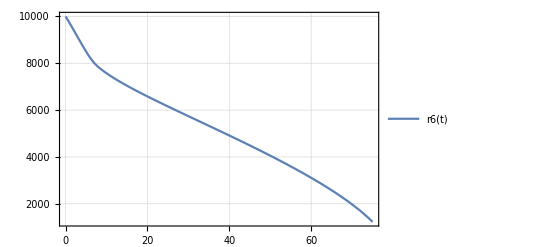

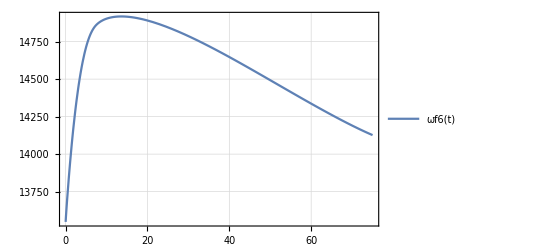

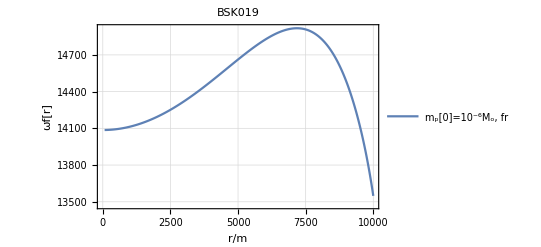

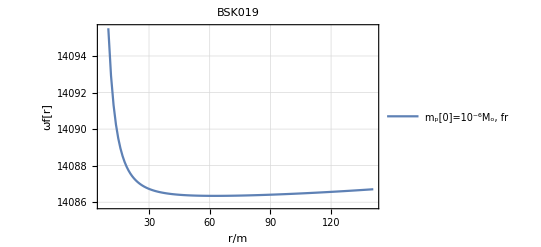

```mathematica
Plot[r6[t],{t,0,75},PlotTheme->"Detailed",PlotRange->All]
(*Plot[ωa[r],{r,1000,10000},PlotTheme->"Detailed",PlotRange->All]*)
Plot[{ωf6[t]},{t,0,75},PlotTheme->"Detailed",PlotRange->All]
ListPlot[{Table[{r6[t],ωf6[t]},{t,0,79.44,0.05}]},Joined->True,PlotTheme->"Detailed",PlotLegends->Placed[LineLegend[{
Style["m_p[0]=10^-6M_o, fr",16,Black,FontFamily->"Times New Roman"],
Style["m_p[0]=10^-6M_o, no-fr",16,Black,FontFamily->"Times New Roman"]
},LegendFunction->Frame],After],PlotLabel->Style["BSK019",16,Black,FontFamily->"Times New Roman"],
FrameLabel->{Style["r/m",16,Black,FontFamily->"Times New Roman"],Style["ωf[r]",16,Black,FontFamily->"Times New Roman"]}]
ListPlot[{Table[{r6[t],ωf6[t]},{t,79.3,79.4435,0.0005}]},PlotRange->Full,Joined->True,PlotTheme->"Detailed",PlotLegends->Placed[LineLegend[{
Style["m_p[0]=10^-6M_o, fr",16,Black,FontFamily->"Times New Roman"],
Style["m_p[0]=10^-6M_o, no-fr",16,Black,FontFamily->"Times New Roman"]
},LegendFunction->Frame],After],PlotLabel->Style["BSK019",16,Black,FontFamily->"Times New Roman"],
FrameLabel->{Style["r/m",16,Black,FontFamily->"Times New Roman"],Style["ωf[r]",16,Black,FontFamily->"Times New Roman"]}]
```

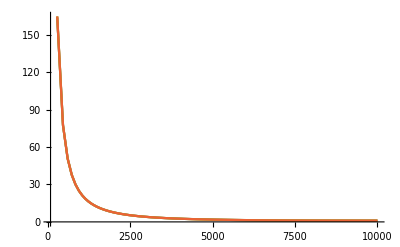

```mathematica
ListPlot[{Table[{r3[t],mp3[t]/mp3[0]},{t,0,0.079,0.0005}],Table[{r4[t],mp4[t]/mp4[0]},{t,0,0.79,0.005}],Table[{r5[t],mp5[t]/mp5[0]},{t,0,7.9,0.05}],Table[{r6[t],mp6[t]/mp6[0]},{t,0,79,0.5}]},PlotRange->Full,Joined->True]
```

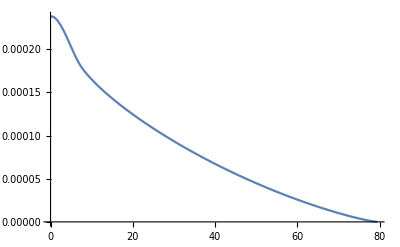

```mathematica
Plot[(4 r6[t]^2 ω1[r6[t]]^2)/(10^4 pc),{t,0,79.44}]
```

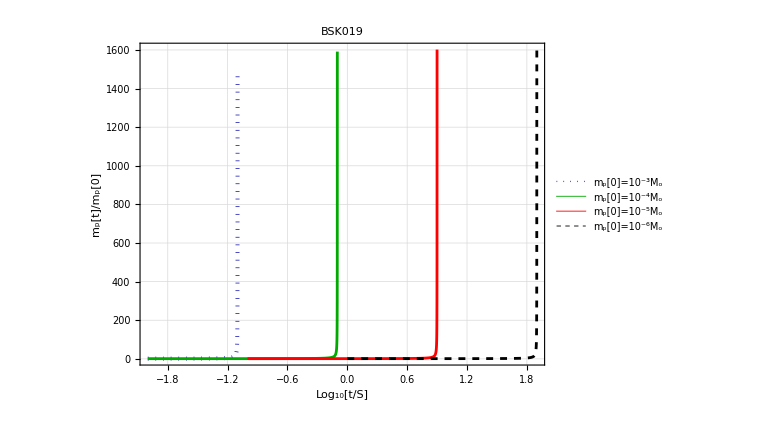

```mathematica
ListPlot[{Table[{Log10[t],mp3[t]/mp3[0]},{t,0.01,0.0794,0.0001}],Table[{Log10[t],mp4[t]/mp4[0]},{t,0.01,0.7944,0.001}],Table[{Log10[t],mp5[t]/mp5[0]},{t,0.1,7.944,0.01}],Table[{Log10[t],mp6[t]/mp6[0]},{t,1,79.44,0.1}]
},Joined->True,PlotRange->All,
Frame->True,GridLines->Automatic,
PlotStyle->{
Directive[Darker[Blue],Dotted,Thickness[0.005]],
Directive[Darker[Green],0,Thickness[0.0035]],
Directive[Red,0,Thickness[0.0035]],
Directive[Black,Dashed,Thickness[0.0035]]},
PlotLegends->Placed[LineLegend[{
Style["m_p[0]=10^-3M_o",20,Black,FontFamily->"Times New Roman"],
Style["m_p[0]=10^-4M_o",20,Black,FontFamily->"Times New Roman"],
Style["m_p[0]=10^-5M_o",20,Black,FontFamily->"Times New Roman"],
Style["m_p[0]=10^-6M_o",20,Black,FontFamily->"Times New Roman"]
},LegendFunction->Frame],After],PlotLabel->Style["BSK019",32,Black,FontFamily->"Times New Roman"],
FrameLabel->{Style["Log_10[t/S]",25,FontFamily->"Times New Roman"],Style["m_p[t]/m_p[0]",25,Black,FontFamily->"Times New Roman"]},FrameTicks->True,FrameStyle->Directive[Black,Thickness[0.005],25],ImageSize->Large,AspectRatio->3/4]
```

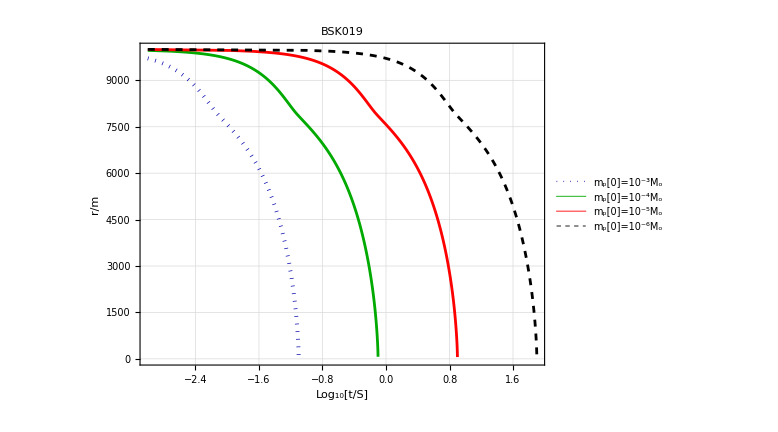

```mathematica
ListPlot[{Table[{Log10[t],r3[t]},{t,0.001,0.07944,0.0001}],
Table[{Log10[t],r4[t]},{t,0.001,0.7944,0.001}],
Table[{Log10[t],r5[t]},{t,0.001,7.944,0.01}],
Table[{Log10[t],r6[t]},{t,0.001,79.44,0.1}]
},Joined->True,PlotRange->All,
Frame->True,GridLines->Automatic,
PlotStyle->{
Directive[Darker[Blue],Dotted,Thickness[0.005]],
Directive[Darker[Green],0,Thickness[0.0035]],
Directive[Red,0,Thickness[0.0035]],
Directive[Black,Dashed,Thickness[0.0035]]},
PlotLegends->Placed[LineLegend[{
Style["m_p[0]=10^-3M_o",20,Black,FontFamily->"Times New Roman"],
Style["m_p[0]=10^-4M_o",20,Black,FontFamily->"Times New Roman"],
Style["m_p[0]=10^-5M_o",20,Black,FontFamily->"Times New Roman"],
Style["m_p[0]=10^-6M_o",20,Black,FontFamily->"Times New Roman"]
},LegendFunction->Frame],After],PlotLabel->Style["BSK019",32,Black,FontFamily->"Times New Roman"],
FrameLabel->{Style["Log_10[t/S]",25,FontFamily->"Times New Roman"],Style["r/m",25,Black,FontFamily->"Times New Roman"]},FrameTicks->True,FrameStyle->Directive[Black,Thickness[0.005],25],ImageSize->Large,AspectRatio->3/4]
```

### Comparing with others

```mathematica
(* dϵ=dE/μ mp=10^{-3}*)
NDSolve[{mp'[t]==dmpdt[t],r'[t]==(dϵdtgfa0[t]+dϵdtgdf[t]+gwdϵdt2[t])/(doEdr2[t]),r[0]==10000,mp[0]==10^-3 Msun},{mp,r},{t,0, 0.08037377},(*Method->{"EquationSimplification"->Automatic},*)(*Method->{"Extrapolation",Method->"ExplicitModifiedMidpoint"},*)(*Method->"StiffnessSwitching",*)MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12]
```

{{mp→InterpolatingFunction[…],r→InterpolatingFunction[…]}}

```mathematica
mp33[t_]=mp[t]/.mp->InterpolatingFunction[…];
r33[t_]=r[t]/.r->InterpolatingFunction[…];
```

```mathematica
{mp33[ 0.08]/mp33[0],mp33[ 0.08037]/mp33[0],mp33[ 0.08037377]/mp33[0]}
{r33[ 0.08],r33[ 0.08037],r33[ 0.08037377]}
```

{196.313,19413.,7.8873×10^6}

{706.944,98.2354,17.4204}

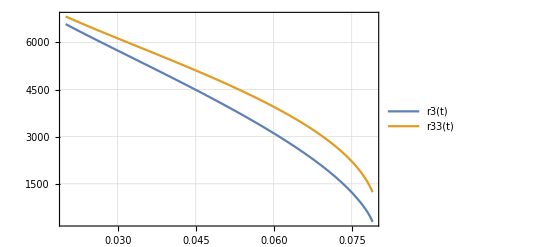

```mathematica
Plot[{r3[t],r33[t]},{t,0.02,0.079},PlotTheme->"Detailed",PlotRange->All]
```

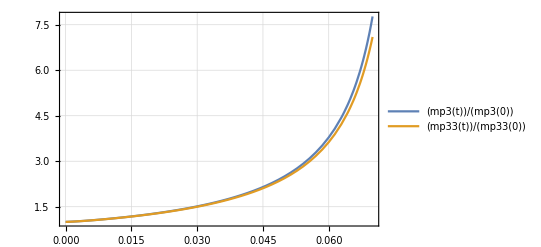

```mathematica
Plot[{mp3[t]/mp3[0],mp33[t]/mp33[0]},{t,0,0.07},PlotTheme->"Detailed",PlotRange->All]
```

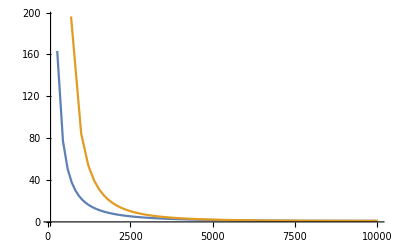

```mathematica
ListPlot[{Table[{r3[t],mp3[t]/mp3[0]},{t,0,0.079,0.0005}],Table[{r33[t],mp33[t]/mp33[0]},{t,0,0.08,0.0005}]},PlotRange->Full,Joined->True]
```

```mathematica
NDSolve[{mp'[t]==dmpdt[t],r'[t]==(dϵdtgfa0[t]+dϵdtgdf[t]+gwdϵdt2[t])/(doEdr2[t]),r[0]==10000,mp[0]==10^-6 Msun},{mp,r},{t,0,80.3694},MaxSteps->∞,AccuracyGoal->12,PrecisionGoal->12]
```

{{mp→InterpolatingFunction[…],r→InterpolatingFunction[…]}}

```mathematica
mp66[t_]=mp[t]/.mp->InterpolatingFunction[…];
r66[t_]=r[t]/.r->InterpolatingFunction[…];
```

```mathematica
{mp66[ 80]/mp66[0],mp66[ 80.36]/mp66[0],mp66[ 80.369]/mp66[0]}
{r66[ 80],r66[ 80.3],r66[ 80.369]}
```

{198.634,7795.02,178019.}

{703.363,343.752,37.3445}

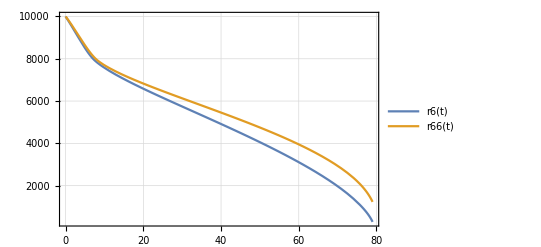

```mathematica
Plot[{r6[t],r66[t]},{t,0,79},PlotTheme->"Detailed",PlotRange->All]
```

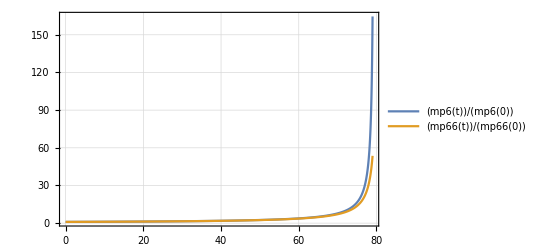

```mathematica
Plot[{mp6[t]/mp6[0],mp66[t]/mp66[0]},{t,0,79},PlotTheme->"Detailed",PlotRange->All]
```

```mathematica
ListPlot[{Table[{r22[t],mp22[t]/mp22[0]},{t,0,0.079,0.0005}],Table[{r33[t],mp33[t]/mp33[0]},{t,0,0.08,0.0005}]},PlotRange->Full,Joined->True]
```

-Graphics-

### Caculations

ds^2=-A(r)dt^2+B(r)dr^2+r^2(dθ^2+Sin[θ]^2 dϕ^2)=-f(r)ⅆ t^2+(1-(2m(r))/r)^-1 ⅆ r^2+r^2(ⅆ θ^2+Sin[θ]^2 ⅆ ϕ^2)
( A=f(r)=ⅇ^(2 α[r]), B=(1-(2m(r))/r)^-1 )

g_tt=-A;g_rr=B;g_ϕϕ=r^2;
μ_0=ⅇ, μ_ϕ=h;
E=-u_0=-g_tt u^t=A u^t=A ⅆt/ⅆτ;
L=u_ϕ=g_ϕϕ u^ϕ=r^2 u^ϕ=r^2 ⅆϕ/ⅆτ;
( μ^t=ⅆt/ⅆτ,μ^r=ⅆr/ⅆτ,u^ϕ=ⅆϕ/ⅆτ )

L=(r^(3/2) √A')/(√(2 A-r A'));
E=(√2 A)/(√(2 A-r A'));
ω=ⅆϕ/ⅆt=u^ϕ/u^t=(L A)/(E r^2)=√(A'/(2r));

J=μ L=μ(r^(3/2) √A')/(√(2 A-r A'))
ⅆJ/ⅆτ=ⅆJ/ⅆt ⅆt/ⅆτ=0
⟹ⅆJ/ⅆt=ⅆμ/ⅆt L+μ ⅆL/ⅆr ⅆr/ⅆt=0
⟹ⅆr/ⅆt=-ⅆμ/ⅆt 1/μ L(ⅆL/ⅆr)^-1;
ϵ=μ E=μ (√2 A)/(√(2 A-r A'));
ⅆϵ/ⅆt=ⅆμ/ⅆt E+μ ⅆE/ⅆr ⅆr/ⅆt=ⅆμ/ⅆt E+μ ⅆE/ⅆr(-ⅆμ/ⅆt 1/μ L(ⅆL/ⅆr)^-1)
=ⅆμ/ⅆt (E-ⅆE/ⅆr L(ⅆL/ⅆr)^-1);
E-ⅆE/ⅆr L(ⅆL/ⅆr)^-1= (√2 A)/(√(2 A-r A'))-(ⅆ/ⅆr(√2 A)/(√(2 A-r A')))(r^(3/2) √A')/(√(2 A-r A'))(ⅆ/ⅆr(r^(3/2) √A')/(√(2 A-r A')))^-1=(√2 A)/(√(2 A-r A'))-(r A'[r])/(√(4 A[r]-2 r A'[r]))=√(A[r]-1/2 r A'[r]);
Thus,
P_a=ⅆμ/ⅆt √(A[r]-1/2 r A'[r])
=ⅆμ/ⅆt √(A[r]-r A[r] α'[r]);
pa=ⅆμ/ⅆt(-(r A'[r])/(√(4 A[r]-2 r A'[r])))
=-ⅆμ/ⅆt(r α'[r]√(A[r]/(1-r α'[r])))
(A(r)=ⅇ^(2 α[r]))